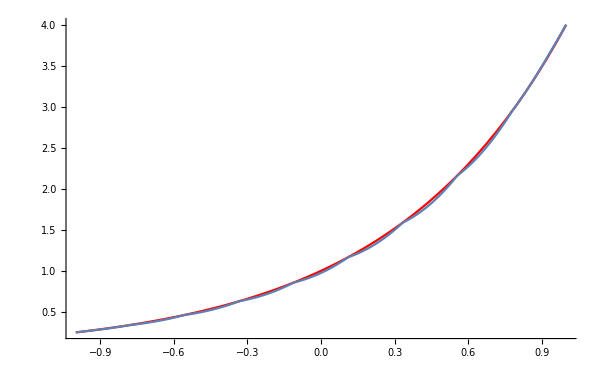

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
list1 = ReadList["uniform.txt", Number, RecordLists->True];
list2 = ReadList["chebysh.txt", Number, RecordLists->True];
uni = Partition[Riffle[list1[[1]], list1[[2]]], 2];
cheb = Partition[Riffle[list2[[1]], list2[[2]]], 2];
list3= ReadList["spline.txt", Number, RecordLists->True];
n=list3[[1,1]];
listplot={};
For[i=1,i<n,i++,
spline=list3[[i+1,1]]+list3[[i+1,2]]*(x-list1[[1,i]])+list3[[i+1,3]]*(x-list1[[1,i]])^2+list3[[i+1,4]]*(x-list1[[1,i]])^3;
plot=Plot[spline==0,{x,list1[[1,i]],list1[[1,i+1]]}];
listplot=Append[listplot,plot];
]
Show[Plot[4^x,{x,-1,1},PlotStyle->Red],listplot,PlotRange->All,ImageSize->600]
```